# Notebook 07: Colour

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Named colours

We have seen that Mathematica understands the names of some colours, like LightBlue and Brown

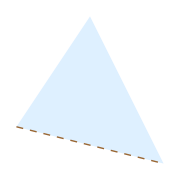

```mathematica
Graphics[{LightBlue,Triangle[{{0,0},{2,3},{4,-1}}],Brown,Thick,Dashed, Line[{{0,0},{4,-1}}]},ImageSize->Small]
```

Here are colour chips for all of the named colours and their lighter variants

```mathematica
namedColours={Red,Blue,Green,Black,White,Gray,Cyan,Magenta,Yellow,Brown,Orange,Pink,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],GrayLevel[0],GrayLevel[1],GrayLevel[0.5],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 1, 0],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.5, 0, 0.5]}

```mathematica
namedLightColours={LightRed,LightBlue,LightGreen,LightGray,LightCyan,LightMagenta,LightYellow,LightBrown,LightOrange,LightPink,LightPurple}
```

{RGBColor[1, 0.85, 0.85],RGBColor[0.87, 0.94, 1],RGBColor[0.88, 1, 0.88],GrayLevel[0.85],RGBColor[0.9, 1, 1],RGBColor[1, 0.9, 1],RGBColor[1, 1, 0.85],RGBColor[0.94, 0.91, 0.88],RGBColor[1, 0.9, 0.8],RGBColor[1, 0.925, 0.925],RGBColor[0.94, 0.88, 0.94]}

When you have a list of named colours like this, you can use RandomChoice to choose one with equal probability

```mathematica
RandomChoice[namedColours]
```

RGBColor[1, 1, 0]

### Randomly coloured objects

Examples of graphics created by randomly choosing colours of rotated and translated objects

```mathematica
Graphics[Table[{RandomChoice[namedColours],Translate[Rotate[Rectangle[{0,0},{.3,5}],r*5Degree],{r/2,0}]},{r,0,120}],ImageSize->Full]
```

-Graphics-

```mathematica
Graphics[Table[{RandomChoice[namedLightColours],EdgeForm[Black],Rotate[Translate[Disk[{0,0},{1,2}],{r/2,r/5}],r*15Degree]},{r,0,60}],ImageSize->Full]
```

-Graphics-

The RandomColor command chooses from a much wider set of possibilities

```mathematica
Graphics[Table[{RandomColor[],Translate[Rotate[Rectangle[{0,0},{.3,10}],r*5Degree],{0,r/4}]},{r,0,80}]]
```

-Graphics-

## RGBColor

We can actually specify an arbitrary colour in a number of different ways. One of the most common methods is to describe the colour as a mixture of Red, Green and Blue, using a number between 0 and 1 for each of the three parameters.

The named colour Red corresponds to RGB values of {1, 0, 0}. RGB values for the named colours Green and Blue can be obtained in a similar way.

```mathematica
RGBColor[1,0,0]
```

RGBColor[1, 0, 0]

```mathematica
RGBColor[0,1,0]
```

RGBColor[0, 1, 0]

```mathematica
RGBColor[0,0,1]
```

RGBColor[0, 0, 1]

We can generate gradients by using Table to vary one or more of the three parameters, as shown in the text

```mathematica
Table[RGBColor[1,g,0],{g,0,1,.05}]
```

{RGBColor[1, 0., 0],RGBColor[1, 0.05, 0],RGBColor[1, 0.1, 0],RGBColor[1, 0.15000000000000002, 0],RGBColor[1, 0.2, 0],RGBColor[1, 0.25, 0],RGBColor[1, 0.30000000000000004, 0],RGBColor[1, 0.35000000000000003, 0],RGBColor[1, 0.4, 0],RGBColor[1, 0.45, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.55, 0],RGBColor[1, 0.6000000000000001, 0],RGBColor[1, 0.65, 0],RGBColor[1, 0.7000000000000001, 0],RGBColor[1, 0.75, 0],RGBColor[1, 0.8, 0],RGBColor[1, 0.8500000000000001, 0],RGBColor[1, 0.9, 0],RGBColor[1, 0.9500000000000001, 0],RGBColor[1, 1., 0]}

### Colour grids

If we vary two of the parameters at once, we get a grid of possibilities.

```mathematica
TableForm[Table[RGBColor[1,g,b],{g,0,1,.1},{b,0,1,.1}]]
```

RGBColor[1, 0., 0.] | RGBColor[1, 0., 0.1] | RGBColor[1, 0., 0.2] | RGBColor[1, 0., 0.30000000000000004] | RGBColor[1, 0., 0.4] | RGBColor[1, 0., 0.5] | RGBColor[1, 0., 0.6000000000000001] | RGBColor[1, 0., 0.7000000000000001] | RGBColor[1, 0., 0.8] | RGBColor[1, 0., 0.9] | RGBColor[1, 0., 1.]
RGBColor[1, 0.1, 0.] | RGBColor[1, 0.1, 0.1] | RGBColor[1, 0.1, 0.2] | RGBColor[1, 0.1, 0.30000000000000004] | RGBColor[1, 0.1, 0.4] | RGBColor[1, 0.1, 0.5] | RGBColor[1, 0.1, 0.6000000000000001] | RGBColor[1, 0.1, 0.7000000000000001] | RGBColor[1, 0.1, 0.8] | RGBColor[1, 0.1, 0.9] | RGBColor[1, 0.1, 1.]
RGBColor[1, 0.2, 0.] | RGBColor[1, 0.2, 0.1] | RGBColor[1, 0.2, 0.2] | RGBColor[1, 0.2, 0.30000000000000004] | RGBColor[1, 0.2, 0.4] | RGBColor[1, 0.2, 0.5] | RGBColor[1, 0.2, 0.6000000000000001] | RGBColor[1, 0.2, 0.7000000000000001] | RGBColor[1, 0.2, 0.8] | RGBColor[1, 0.2, 0.9] | RGBColor[1, 0.2, 1.]
RGBColor[1, 0.30000000000000004, 0.] | RGBColor[1, 0.30000000000000004, 0.1] | RGBColor[1, 0.30000000000000004, 0.2] | RGBColor[1, 0.30000000000000004, 0.30000000000000004] | RGBColor[1, 0.30000000000000004, 0.4] | RGBColor[1, 0.30000000000000004, 0.5] | RGBColor[1, 0.30000000000000004, 0.6000000000000001] | RGBColor[1, 0.30000000000000004, 0.7000000000000001] | RGBColor[1, 0.30000000000000004, 0.8] | RGBColor[1, 0.30000000000000004, 0.9] | RGBColor[1, 0.30000000000000004, 1.]
RGBColor[1, 0.4, 0.] | RGBColor[1, 0.4, 0.1] | RGBColor[1, 0.4, 0.2] | RGBColor[1, 0.4, 0.30000000000000004] | RGBColor[1, 0.4, 0.4] | RGBColor[1, 0.4, 0.5] | RGBColor[1, 0.4, 0.6000000000000001] | RGBColor[1, 0.4, 0.7000000000000001] | RGBColor[1, 0.4, 0.8] | RGBColor[1, 0.4, 0.9] | RGBColor[1, 0.4, 1.]
RGBColor[1, 0.5, 0.] | RGBColor[1, 0.5, 0.1] | RGBColor[1, 0.5, 0.2] | RGBColor[1, 0.5, 0.30000000000000004] | RGBColor[1, 0.5, 0.4] | RGBColor[1, 0.5, 0.5] | RGBColor[1, 0.5, 0.6000000000000001] | RGBColor[1, 0.5, 0.7000000000000001] | RGBColor[1, 0.5, 0.8] | RGBColor[1, 0.5, 0.9] | RGBColor[1, 0.5, 1.]
RGBColor[1, 0.6000000000000001, 0.] | RGBColor[1, 0.6000000000000001, 0.1] | RGBColor[1, 0.6000000000000001, 0.2] | RGBColor[1, 0.6000000000000001, 0.30000000000000004] | RGBColor[1, 0.6000000000000001, 0.4] | RGBColor[1, 0.6000000000000001, 0.5] | RGBColor[1, 0.6000000000000001, 0.6000000000000001] | RGBColor[1, 0.6000000000000001, 0.7000000000000001] | RGBColor[1, 0.6000000000000001, 0.8] | RGBColor[1, 0.6000000000000001, 0.9] | RGBColor[1, 0.6000000000000001, 1.]
RGBColor[1, 0.7000000000000001, 0.] | RGBColor[1, 0.7000000000000001, 0.1] | RGBColor[1, 0.7000000000000001, 0.2] | RGBColor[1, 0.7000000000000001, 0.30000000000000004] | RGBColor[1, 0.7000000000000001, 0.4] | RGBColor[1, 0.7000000000000001, 0.5] | RGBColor[1, 0.7000000000000001, 0.6000000000000001] | RGBColor[1, 0.7000000000000001, 0.7000000000000001] | RGBColor[1, 0.7000000000000001, 0.8] | RGBColor[1, 0.7000000000000001, 0.9] | RGBColor[1, 0.7000000000000001, 1.]
RGBColor[1, 0.8, 0.] | RGBColor[1, 0.8, 0.1] | RGBColor[1, 0.8, 0.2] | RGBColor[1, 0.8, 0.30000000000000004] | RGBColor[1, 0.8, 0.4] | RGBColor[1, 0.8, 0.5] | RGBColor[1, 0.8, 0.6000000000000001] | RGBColor[1, 0.8, 0.7000000000000001] | RGBColor[1, 0.8, 0.8] | RGBColor[1, 0.8, 0.9] | RGBColor[1, 0.8, 1.]
RGBColor[1, 0.9, 0.] | RGBColor[1, 0.9, 0.1] | RGBColor[1, 0.9, 0.2] | RGBColor[1, 0.9, 0.30000000000000004] | RGBColor[1, 0.9, 0.4] | RGBColor[1, 0.9, 0.5] | RGBColor[1, 0.9, 0.6000000000000001] | RGBColor[1, 0.9, 0.7000000000000001] | RGBColor[1, 0.9, 0.8] | RGBColor[1, 0.9, 0.9] | RGBColor[1, 0.9, 1.]
RGBColor[1, 1., 0.] | RGBColor[1, 1., 0.1] | RGBColor[1, 1., 0.2] | RGBColor[1, 1., 0.30000000000000004] | RGBColor[1, 1., 0.4] | RGBColor[1, 1., 0.5] | RGBColor[1, 1., 0.6000000000000001] | RGBColor[1, 1., 0.7000000000000001] | RGBColor[1, 1., 0.8] | RGBColor[1, 1., 0.9] | RGBColor[1, 1., 1.]

We can use the same Table command to generate a grid of rectangles or disks

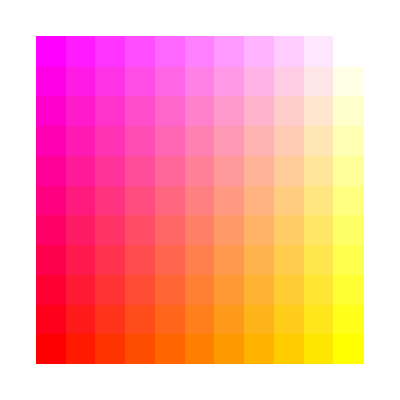

```mathematica
Graphics[Table[{RGBColor[1,g,b],Rectangle[{g*10,b*10},{(g-.1)*10,(b-.1)*10}]},{g,0,1,.1},{b,0,1,.1}]]
```

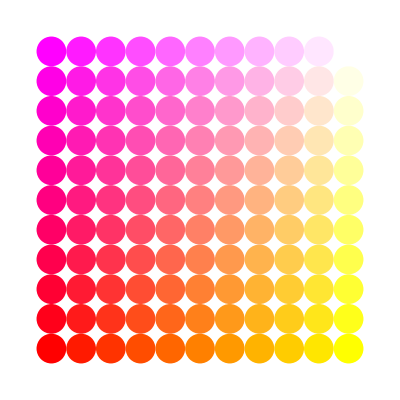

```mathematica
Graphics[Table[{RGBColor[1,g,b],Disk[{g*10,b*10},1/2]},{g,0,1,.1},{b,0,1,.1}]]
```

## ColorSetter and ColorSlider

If you aren’t sure how a colour like Brown is created from a mixture of Red, Green and Blue, it can sometimes be hard to find the parameter values. Mathematica provides access to your operating system’s colour chooser via the ColorSetter and ColorSlider commands. In order to get them to output RGB values, I have included some code that we haven’t learned yet (the Dynamic command). For now, you can just copy one of these expressions when you need to discover RGB values.

```mathematica
ColorSetter[Dynamic[t]]
```

$CellContext`t

```mathematica
ColorSlider[Dynamic[t]]
```

$CellContext`t

Once you find a colour you like, you use InputForm command to get the RGB values

```mathematica
InputForm[t]
```

RGBColor[0., 0., 0.]

## The Blend command

Another way to generate a gradient is with the Blend command. The colour that is 3/8 of the way from Blue to Green is

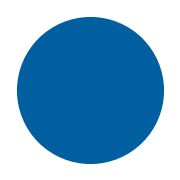

```mathematica
Graphics[{Blend[{Blue,Green},3/8],Disk[]},ImageSize->Small]
```

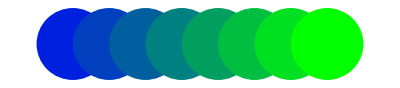

```mathematica
Graphics[Table[{Blend[{Blue,Green},x/8],Disk[{x,0}]},{x,1,8}]]
```

### A more complicated example with Blend

Recall that CirclePoints uses trigonometry to generate evenly spaced positions around a circle. The output is a list of pairs, such as

```mathematica
CirclePoints[3]
```

{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}

The Part command allows us to choose an element from a list. It is usually abbreviated with double square brackets. To make those, use Esc[[Esc and Esc]]Esc

```mathematica
Part[{a,b,c},1]
```

a

```mathematica
{a,b,c}⟦1⟧
```

```mathematica
Part[{a,b,c},2]
```

b

```mathematica
{a,b,c}⟦2⟧
```

b

Study the following example carefully, until you understand how Part and CirclePoints are working together.

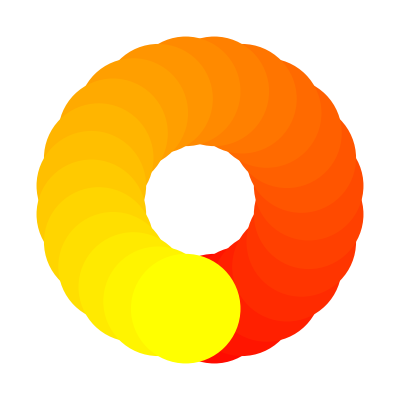

```mathematica
Graphics[Table[{Blend[{Red,Yellow},x/24],Disk[CirclePoints[24]⟦x⟧,1/2]},{x,1,24}]]
```

## Hue

The Hue command gives you a different way to specify colour, by providing parameters for its hue, saturation and brightness / value.

### Changing hue

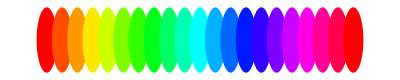

```mathematica
Graphics[Table[{Hue[h,1,1],Disk[{h*10,0},1/3]},{h,0,1,.05}],ImageSize->Full]
```

### Changing saturation

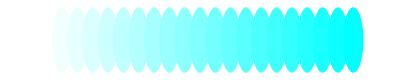

```mathematica
Graphics[Table[{Hue[.5,s,1],Disk[{s*10,0},1/3]},{s,0,1,.05}],ImageSize->Full]
```

### Changing brightness / value

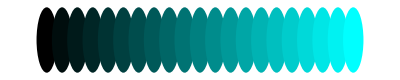

```mathematica
Graphics[Table[{Hue[.5,1,b],Disk[{b*10,0},1/3]},{b,0,1,.05}],ImageSize->Full]
```

### A grid of disks with random brightness

The RandomReal command returns a random value between 0 and 1

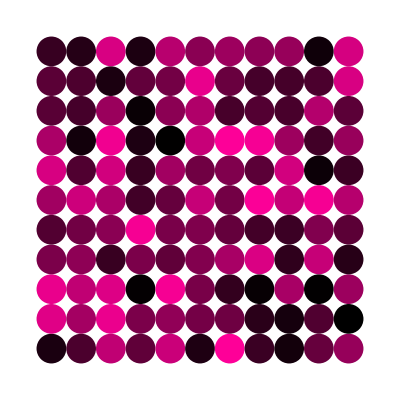

```mathematica
Graphics[Table[{Hue[.9,1,RandomReal[]],Disk[{g*10,b*10},1/2]},{g,0,1,.1},{b,0,1,.1}]]
```

## In-Class Activity

### Draw a picture using the Graphics command. Use Table with RGBColor, Hue and/or Blend to generate a range of colours in your image.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course